```mathematica
Clear["Global`*"]
```

# Fifth order solution

## Cory Aitchison - January 2022

Find the fifth order solutions by solving L[u2 + u1 + u0] + N[u1 + u0] == 0 to 5th order

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
```

```mathematica
(* estimates = {A -> 0.4384, B -> 1.017}; *)
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

```mathematica
answer1 = AnalyticSolve[LDE[u[1]] +LDE[u[0]]+ NDE[u[0]], 1, x, σ, c]
```

{c[0]→A/4-((2 A^3+9 A^2 B+6 A B^2+9 B^3) Γ)/(1280 σ^4),c[1]→-B/4+(3 (3 A^3+2 A^2 B+3 A B^2-2 B^3) Γ)/(1280 σ^4),c[2]→A/4-(3 (2 A^3+3 A^2 B-2 A B^2+3 B^3) Γ)/(1280 σ^4),c[3]→-B/4+((9 A^3-6 A^2 B+9 A B^2-2 B^3) Γ)/(1280 σ^4)}

```mathematica
allvalues= Merge[{param, estimates, answer1 /. estimates /. param}, First]
```

<|σ→6^(1/4),Γ→-24,A→0.4384,B→1.017,c[0]→0.15371,c[1]→-0.253315,c[2]→0.137759,c[3]→-0.259133|>

## Full Solution

```mathematica
eq1 := LDE[x |-> u[2][x] + u[1][x] + u[0][x]] + NDE[x |->u[0][x] + u[1][x]] ;
```

```mathematica
answer2 =AnalyticSolve[eq1 /. answer1, 2, x, σ, d] // FullSimplify
```

{d[0]→A/8+((-95 A^5+86 A^4 B+98 A^3 B^2+352 A^2 B^3+273 A B^4+266 B^5) Γ^2)/(21299200 σ^8)-(3 (2 A^3+9 A^2 B+6 A B^2+9 B^3) Γ)/(5120 σ^4),d[1]→-B/8-((86 A^5+671 A^4 B+712 A^3 B^2+798 A^2 B^3+626 A B^4-273 B^5) Γ^2)/(21299200 σ^8)+(3 (3 A^3+2 A^2 B+3 A B^2-2 B^3) Γ)/(5120 σ^4),d[2]→1/(10649600 σ^8)Γ ((49 A^5+356 A^4 B+50 A^3 B^2+532 A^2 B^3-399 A B^4+176 B^5) Γ-12480 B (3 A^2+4 A B+3 B^2) σ^4),d[3]→1/(10649600 σ^8)Γ (-((176 A^5+399 A^4 B+532 A^3 B^2-50 A^2 B^3+356 A B^4-49 B^5) Γ)-12480 A (3 A^2-4 A B+3 B^2) σ^4),d[4]→-A/8+((273 A^5+626 A^4 B-798 A^3 B^2+712 A^2 B^3-671 A B^4+86 B^5) Γ^2)/(21299200 σ^8)+(3 (2 A^3+3 A^2 B-2 A B^2+3 B^3) Γ)/(5120 σ^4),d[5]→B/8-((266 A^5-273 A^4 B+352 A^3 B^2-98 A^2 B^3+86 A B^4+95 B^5) Γ^2)/(21299200 σ^8)+(3 (-9 A^3+6 A^2 B-9 A B^2+2 B^3) Γ)/(5120 σ^4)}

```mathematica
answer2 //. allvalues
```

{d[0]→0.088257,d[1]→-0.127076,d[2]→0.0262384,d[3]→0.00364435,d[4]→-0.061929,d[5]→0.130676}

## Step by Step

```mathematica
notrig = {
Cosh[_] -> cosh, Sinh[_]->sinh,
Tanh[_] -> sinh / cosh, Coth[_] -> cosh / sinh, 
Sech[_] -> 1/cosh,  Csch[_] -> 1/sinh
};
```

```mathematica
eq2 := (eq1  /. answer1) //. notrig // Together;
```

```mathematica
Denominator[eq2]
```

2097152000 cosh^9 sinh^9 σ^12

```mathematica
eq3 := Numerator[eq2];
```

We can then use hyp trig identity cosh^2 - sinh^2 = 1 to reduce the terms further.

```mathematica
htrigident = {
cosh^k_-> (1+sinh^2)^(Floor[k/2]) cosh^(Mod[k,2])
};
```

```mathematica
eq4 := eq3 //. htrigident//Expand;
```

### Extracting Coefficients

Now that it is all simplified as far as possible, we can extract the coefficients that give us 13th powers (for the numerator). There will be two: cosh * sinh^12, and sinh^13.

```mathematica
list1 := CoefficientList[eq4, {sinh, cosh}];
```

Check that the lower order terms are 0:

```mathematica
{ list1[[15]], list1[[16]]} // Simplify
```

{{0,0},{0,0}}

```mathematica
list2 := {
list1[[13,2]], (* sinh^12 cosh^1 *)
list1[[14,1]]     (* sinh^13 cosh^0 *)
};
```

### Simplifying Trig

These two terms should be identically zero. To find the conditions on c[...], we need to simplify the trig terms using identities:

```mathematica
trigident = {
Cos[x σ]^k_-> (1-Sin[x σ]^2)^(Floor[k/2]) Cos[x σ]^(Mod[k,2])
};
```

```mathematica
list3 :=CoefficientList[list2 /. trigident, {Cos[x σ], Sin[x σ]}];
```

We select only the nonzero coefficients which we need to solve for:

```mathematica
(list4 = list3 // Flatten // Select[Not@*PossibleZeroQ]) // MatrixForm
```

(44236800 A^5 Γ^2 σ^8+9830400 A^4 B Γ^2 σ^8-44236800 A^3 B^2 Γ^2 σ^8-88473600 A^2 B^3 Γ^2 σ^8-88473600 A B^4 Γ^2 σ^8+14745600000 A^3 Γ σ^12+8847360000 A^2 B Γ σ^12+17104896000 A B^2 Γ σ^12+11206656000 B^3 Γ σ^12-440401920000 A σ^16-314572800000 B σ^16+2516582400000 σ^16 d[0]-2264924160000 σ^16 d[1]-251658240000 σ^16 d[2]+1509949440000 σ^16 d[3]-1006632960000 σ^16 d[4]+251658240000 σ^16 d[5]
-44236800 A^5 Γ^2 σ^8-108134400 A^4 B Γ^2 σ^8+88473600 A^3 B^2 Γ^2 σ^8+255590400 A^2 B^3 Γ^2 σ^8+132710400 A B^4 Γ^2 σ^8-29491200 B^5 Γ^2 σ^8-14155776000 A^3 Γ σ^12-11010048000 A^2 B Γ σ^12-14155776000 A B^2 Γ σ^12-11010048000 B^3 Γ σ^12+503316480000 A σ^16+335544320000 B σ^16-2516582400000 σ^16 d[0]+7549747200000 σ^16 d[1]+503316480000 σ^16 d[2]-6207569920000 σ^16 d[3]+1509949440000 σ^16 d[4]+4865392640000 σ^16 d[5]
98304000 A^4 B Γ^2 σ^8-196608000 A^2 B^3 Γ^2 σ^8+19660800 B^5 Γ^2 σ^8-5234491392000 σ^16 d[1]+5234491392000 σ^16 d[3]-5234491392000 σ^16 d[5]
-9830400 A^5 Γ^2 σ^8-44236800 A^4 B Γ^2 σ^8-29491200 A^3 B^2 Γ^2 σ^8-44236800 A^2 B^3 Γ^2 σ^8-196608000 A^3 Γ σ^12+2949120000 A^2 B Γ σ^12+2162688000 A B^2 Γ σ^12+589824000 B^3 Γ σ^12+20971520000 A σ^16-62914560000 B σ^16-117440512000 σ^16 d[0]-503316480000 σ^16 d[1]+536870912000 σ^16 d[2]-251658240000 σ^16 d[3]+50331648000 σ^16 d[4]
-9830400 A^5 Γ^2 σ^8+132710400 A^4 B Γ^2 σ^8+137625600 A^3 B^2 Γ^2 σ^8+88473600 A^2 B^3 Γ^2 σ^8-88473600 A B^4 Γ^2 σ^8-44236800 B^5 Γ^2 σ^8-11010048000 A^3 Γ σ^12+14155776000 A^2 B Γ σ^12-11010048000 A B^2 Γ σ^12+14155776000 B^3 Γ σ^12-335544320000 A σ^16+503316480000 B σ^16+5603590144000 σ^16 d[0]+1509949440000 σ^16 d[1]-4261412864000 σ^16 d[2]+503316480000 σ^16 d[3]+2919235584000 σ^16 d[4]-2516582400000 σ^16 d[5]
19660800 A^5 Γ^2 σ^8-196608000 A^3 B^2 Γ^2 σ^8+98304000 A B^4 Γ^2 σ^8-5234491392000 σ^16 d[0]+5234491392000 σ^16 d[2]-5234491392000 σ^16 d[4])

### Solution

```mathematica
answer = Solve[list4 == 0, (i|->d[i])/@ Range[0,5]][[1]] // Simplify
```

{d[0]→1/(21299200 σ^8)(-95 A^5 Γ^2+86 A^4 B Γ^2+2 B^3 Γ (133 B^2 Γ-56160 σ^4)+2 A^3 Γ (49 B^2 Γ-12480 σ^4)+32 A^2 B Γ (11 B^2 Γ-3510 σ^4)+13 A (21 B^4 Γ^2-5760 B^2 Γ σ^4+204800 σ^8)),d[1]→1/(21299200 σ^8)(-86 A^5 Γ^2-671 A^4 B Γ^2-8 A^3 Γ (89 B^2 Γ-4680 σ^4)+6 A^2 B Γ (-133 B^2 Γ+4160 σ^4)+A (-626 B^4 Γ^2+37440 B^2 Γ σ^4)+13 B (21 B^4 Γ^2-1920 B^2 Γ σ^4-204800 σ^8)),d[2]→1/(10649600 σ^8)Γ (49 A^5 Γ+356 A^4 B Γ+50 A^3 B^2 Γ+176 B^5 Γ-37440 B^3 σ^4+4 A^2 (133 B^3 Γ-9360 B σ^4)-3 A (133 B^4 Γ+16640 B^2 σ^4)),d[3]→-1/(10649600 σ^8)Γ (176 A^5 Γ+399 A^4 B Γ-49 B^5 Γ+4 A^3 (133 B^2 Γ+9360 σ^4)-10 A^2 (5 B^3 Γ+4992 B σ^4)+4 A (89 B^4 Γ+9360 B^2 σ^4)),d[4]→1/(21299200 σ^8)(273 A^5 Γ^2+626 A^4 B Γ^2+6 A^3 Γ (-133 B^2 Γ+4160 σ^4)+8 A^2 B Γ (89 B^2 Γ+4680 σ^4)+2 B^3 Γ (43 B^2 Γ+18720 σ^4)-A (671 B^4 Γ^2+24960 B^2 Γ σ^4+2662400 σ^8)),d[5]→1/(21299200 σ^8)(-266 A^5 Γ^2+273 A^4 B Γ^2-95 B^5 Γ^2+24960 B^3 Γ σ^4+2662400 B σ^8-32 A^3 Γ (11 B^2 Γ+3510 σ^4)+2 A^2 B Γ (49 B^2 Γ+37440 σ^4)-2 A B^2 Γ (43 B^2 Γ+56160 σ^4))}

```mathematica
answer /. answer1 // FullSimplify // Apart
```

{d[0]→A/8-((95 A^5-86 A^4 B-98 A^3 B^2-352 A^2 B^3-273 A B^4-266 B^5) Γ^2)/(21299200 σ^8)-(3 (2 A^3+9 A^2 B+6 A B^2+9 B^3) Γ)/(5120 σ^4),d[1]→-B/8+((-86 A^5-671 A^4 B-712 A^3 B^2-798 A^2 B^3-626 A B^4+273 B^5) Γ^2)/(21299200 σ^8)-(3 (-3 A^3-2 A^2 B-3 A B^2+2 B^3) Γ)/(5120 σ^4),d[2]→((49 A^5+356 A^4 B+50 A^3 B^2+532 A^2 B^3-399 A B^4+176 B^5) Γ^2)/(10649600 σ^8)-(3 B (3 A^2+4 A B+3 B^2) Γ)/(2560 σ^4),d[3]→-((176 A^5+399 A^4 B+532 A^3 B^2-50 A^2 B^3+356 A B^4-49 B^5) Γ^2)/(10649600 σ^8)-(3 A (3 A^2-4 A B+3 B^2) Γ)/(2560 σ^4),d[4]→-A/8+((273 A^5+626 A^4 B-798 A^3 B^2+712 A^2 B^3-671 A B^4+86 B^5) Γ^2)/(21299200 σ^8)+(3 (2 A^3+3 A^2 B-2 A B^2+3 B^3) Γ)/(5120 σ^4),d[5]→B/8-((266 A^5-273 A^4 B+352 A^3 B^2-98 A^2 B^3+86 A B^4+95 B^5) Γ^2)/(21299200 σ^8)+(3 (-9 A^3+6 A^2 B-9 A B^2+2 B^3) Γ)/(5120 σ^4)}

```mathematica
answer //. allvalues
```

{d[0]→0.088257,d[1]→-0.127076,d[2]→0.0262384,d[3]→0.00364435,d[4]→-0.061929,d[5]→0.130676}

# Higher Order Solutions

## Set up

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

## Coefficients

```mathematica
answer[1] = GetSolution[1]
```

{c[0]→A/4-((2 A^3+9 A^2 B+6 A B^2+9 B^3) Γ)/(1280 σ^4),c[1]→-B/4+(3 (3 A^3+2 A^2 B+3 A B^2-2 B^3) Γ)/(1280 σ^4),c[2]→A/4-(3 (2 A^3+3 A^2 B-2 A B^2+3 B^3) Γ)/(1280 σ^4),c[3]→-B/4+((9 A^3-6 A^2 B+9 A B^2-2 B^3) Γ)/(1280 σ^4)}

```mathematica
answer[2] = GetSolution[2]
```

{d[0]→A/8+((-95 A^5+86 A^4 B+98 A^3 B^2+352 A^2 B^3+273 A B^4+266 B^5) Γ^2)/(21299200 σ^8)-(3 (2 A^3+9 A^2 B+6 A B^2+9 B^3) Γ)/(5120 σ^4),d[1]→-B/8-((86 A^5+671 A^4 B+712 A^3 B^2+798 A^2 B^3+626 A B^4-273 B^5) Γ^2)/(21299200 σ^8)+(3 (3 A^3+2 A^2 B+3 A B^2-2 B^3) Γ)/(5120 σ^4),d[2]→(Γ ((49 A^5+356 A^4 B+50 A^3 B^2+532 A^2 B^3-399 A B^4+176 B^5) Γ-12480 B (3 A^2+4 A B+3 B^2) σ^4))/(10649600 σ^8),d[3]→(Γ (-((176 A^5+399 A^4 B+532 A^3 B^2-50 A^2 B^3+356 A B^4-49 B^5) Γ)-12480 A (3 A^2-4 A B+3 B^2) σ^4))/(10649600 σ^8),d[4]→-A/8+((273 A^5+626 A^4 B-798 A^3 B^2+712 A^2 B^3-671 A B^4+86 B^5) Γ^2)/(21299200 σ^8)+(3 (2 A^3+3 A^2 B-2 A B^2+3 B^3) Γ)/(5120 σ^4),d[5]→B/8-((266 A^5-273 A^4 B+352 A^3 B^2-98 A^2 B^3+86 A B^4+95 B^5) Γ^2)/(21299200 σ^8)+(3 (-9 A^3+6 A^2 B-9 A B^2+2 B^3) Γ)/(5120 σ^4)}

```mathematica
answer[3] = GetSolution[3];
```

```mathematica
answer[4] = GetSolution[4];
```

```mathematica
answer[5] = GetSolution[5];
```

```mathematica
answer[6] = GetSolution[6];
```

```mathematica
answer[7] = GetSolution[7];
```

$Aborted

```mathematica
answer[7]
```

```mathematica
DumpSave["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx", answer]
```

{answer}

## Patterns

### Linear Terms

```mathematica
ShowLinear[6]
```

(A/4 | A/8 | (5 A)/64 | (7 A)/128 | (21 A)/512 | (33 A)/1024
-B/4 | -B/8 | -(5 B)/64 | -(7 B)/128 | -(21 B)/512 | -(33 B)/1024
A/4 | 0 | -A/64 | -A/64 | -(7 A)/512 | -(3 A)/256
-B/4 | 0 | B/64 | B/64 | (7 B)/512 | (3 B)/256
_ | -A/8 | -A/64 | 0 | A/256 | (5 A)/1024
_ | B/8 | B/64 | 0 | -B/256 | -(5 B)/1024
_ | _ | (5 A)/64 | A/64 | A/256 | 0
_ | _ | -(5 B)/64 | -B/64 | -B/256 | 0
_ | _ | _ | -(7 A)/128 | -(7 A)/512 | -(5 A)/1024
_ | _ | _ | (7 B)/128 | (7 B)/512 | (5 B)/1024
_ | _ | _ | _ | (21 A)/512 | (3 A)/256
_ | _ | _ | _ | -(21 B)/512 | -(3 B)/256
_ | _ | _ | _ | _ | -(33 A)/1024
_ | _ | _ | _ | _ | (33 B)/1024)

```mathematica
ToString[#]/1024&/@((First[(x |-> PadRight[x, 2 + 2*6,  _])/@GetLinear/@ (answer[#]&/@Range[1,6]) // Transpose]  ) * 1024 /. {A->1})
```

{256/1024,128/1024,80/1024,56/1024,42/1024,33/1024}

```mathematica
ToString[#]/1024&/@((First[(x |-> PadRight[x, 2 + 2*6,  _])/@GetLinear/@ (answer[#]&/@Range[1,6]) // Transpose]//Differences  ) * 1024 /. {A->1})
```

{-128/1024,-48/1024,-24/1024,-14/1024,-9/1024}

```mathematica
ToString[#]/1024&/@((First[(x |-> PadRight[x, 2 + 2*6,  _])/@GetLinear/@ (answer[#]&/@Range[1,6]) // Transpose]  // Accumulate) * 1024 /. {A->1})
```

{256/1024,384/1024,464/1024,520/1024,562/1024,595/1024}

### Values

```mathematica
ShowValues[6]
```

(c[0]→0.157039 | d[0]→0.0903383 | e[0]→0.0609978 | f[0]→0.0448517 | g[0]→0.0348072 | h[0]→0.0280441
c[1]→-0.256215 | d[1]→-0.128514 | e[1]→-0.0804295 | f[1]→-0.0563353 | g[1]→-0.0422631 | h[1]→-0.0332103
c[2]→0.140487 | d[2]→0.0271894 | e[2]→0.00526498 | f[2]→-0.00152474 | g[2]→-0.00390647 | h[2]→-0.00469792
c[3]→-0.262153 | d[3]→0.00377046 | e[3]→0.0168306 | f[3]→0.0162891 | g[3]→0.0141419 | h[3]→0.0120898
_ | d[4]→-0.0630543 | e[4]→-0.0190443 | f[4]→-0.00858966 | g[4]→-0.00390552 | h[4]→-0.0014936
_ | d[5]→0.132236 | e[5]→0.0142077 | f[5]→-0.000842331 | g[5]→-0.00440549 | h[5]→-0.00521731
_ | _ | e[6]→0.0366884 | f[6]→0.0133825 | g[6]→0.00733371 | h[6]→0.00430593
_ | _ | e[7]→-0.0830518 | f[7]→-0.015152 | g[7]→-0.00337559 | h[7]→0.000378755
_ | _ | _ | f[8]→-0.0244042 | g[8]→-0.00985882 | h[8]→-0.00593467
_ | _ | _ | f[9]→0.0583147 | g[9]→0.0136075 | h[9]→0.00456695
_ | _ | _ | _ | g[10]→0.0176156 | h[10]→0.00757355
_ | _ | _ | _ | g[11]→-0.0438274 | h[11]→-0.0118415
_ | _ | _ | _ | _ | h[12]→-0.0134343
_ | _ | _ | _ | _ | h[13]→0.0344878)

```mathematica
(((x |-> PadRight[x, 2 + 2*6,  _])/@GetLinear/@ (answer[#]&/@Range[1,6]) // Transpose) /. param /. estimates )// MatrixForm
```

(0.111352 | 0.055676 | 0.0347975 | 0.0243583 | 0.0182687 | 0.014354
-0.257043 | -0.128521 | -0.0803258 | -0.056228 | -0.042171 | -0.0331344
0.111352 | 0 | -0.0069595 | -0.0069595 | -0.00608956 | -0.00521963
-0.257043 | 0 | 0.0160652 | 0.0160652 | 0.014057 | 0.0120489
_ | -0.055676 | -0.0069595 | 0 | 0.00173988 | 0.00217484
_ | 0.128521 | 0.0160652 | 0 | -0.00401629 | -0.00502036
_ | _ | 0.0347975 | 0.0069595 | 0.00173988 | 0
_ | _ | -0.0803258 | -0.0160652 | -0.00401629 | 0
_ | _ | _ | -0.0243583 | -0.00608956 | -0.00217484
_ | _ | _ | 0.056228 | 0.014057 | 0.00502036
_ | _ | _ | _ | 0.0182687 | 0.00521963
_ | _ | _ | _ | -0.042171 | -0.0120489
_ | _ | _ | _ | _ | -0.014354
_ | _ | _ | _ | _ | 0.0331344)

## Plots

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

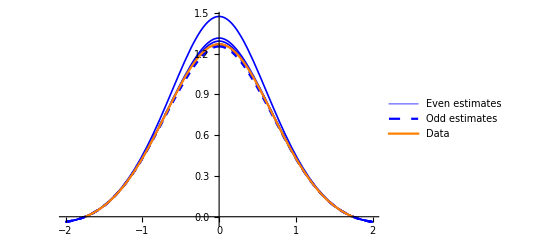

```mathematica
Show[
Plot[{FinalFunction[0], FinalFunction[1], FinalFunction[2], FinalFunction[3], FinalFunction[4], FinalFunction[5]}, {x,-2,2}, PlotStyle->{{Thickness[0.003], Blue}, {Dashed, Blue}}, PlotLegends->{"Even estimates", "Odd estimates"}], 
ListLinePlot[Transpose[{data[[;;,1]], data[[;;,2]]}], PlotStyle->{{Orange, Thick}}, PlotRange->{{-2,2}, {0, 2}}, PlotLegends->{"Data"}]
]
```

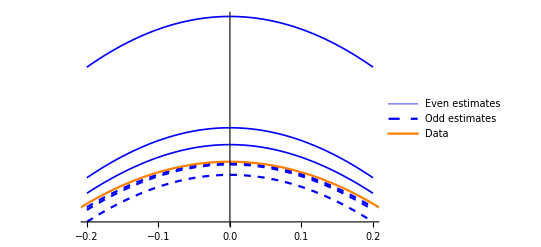

```mathematica
Show[
LogPlot[{FinalFunction[0], FinalFunction[1], FinalFunction[2], FinalFunction[3], FinalFunction[4], FinalFunction[5]}, {x,-0.2,0.2}, PlotStyle->{{Thickness[0.003], Blue}, {Dashed, Blue}}, PlotLegends->{"Even estimates", "Odd estimates"}], 
ListLogPlot[Transpose[{data[[;;,1]], data[[;;,2]]}], PlotStyle->{{Orange, Thick}}, PlotRange->{{-0.5,0.5}, {1, 1.5}}, PlotLegends->{"Data"}, Joined -> True]
]
```

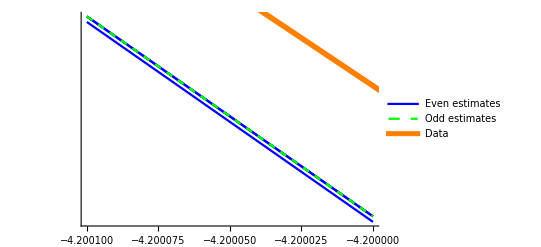

```mathematica
Show[
LogPlot[{FinalFunction[0], FinalFunction[1], FinalFunction[2], FinalFunction[3], FinalFunction[4], FinalFunction[5]}, {x,-4.2001,-4.2}, PlotStyle->{{Thick, Blue}, {Dashed, Green}}, PlotLegends->{"Even estimates", "Odd estimates"}], 
ListLogPlot[Transpose[{data[[;;,1]], data[[;;,2]]}], PlotStyle->{{Orange, Thickness[0.01]}}, PlotRange->{{-5,-4.5}, {0, 1.5}}, PlotLegends->{"Data"}, Joined -> True]
]
```

```mathematica
(Total[Last /@ List @@@ answer[1]] // FullSimplify) /. param /. estimates
```

-0.220843

```mathematica
(Total[Last /@ List @@@ answer[2]] // FullSimplify) /. param /. estimates
```

0.0619659

```mathematica
(Total[Last /@ List @@@ answer[3]] // FullSimplify) /. param /. estimates
```

-0.0485361